```mathematica
Clear[γp,γm]
```

```mathematica
FP[γp_,γm_]:=1/γp^2(Cosh[γp]+γp/γm Sinh[γp]-1)
FM[γp_,γm_]:=FP[γm,γp]
F[γp_,γm_,p_]:=p FP[γp,γm]+(1-p)FM[γp,γm]
GradF[γp_,γm_,p_]:=D[F[zp,zm,p],{{zp,zm}}]/.{zp->γp,zm->γm}
HessianF[γp_,γm_,p_]:=D[F[zp,zm,p],{{zp,zm},2}]/.{zp->γp,zm->γm}
γopt[p_]:={γp,γm}/.FindMinimum[F[γp,γm,p],{{γp,1},{γm,1}},Gradient->GradF[γp,γm,p],Method->{"Newton",Hessian->HessianF[γp,γm,p]}][[2]] 
Fopt[p_]:=FindMinimum[F[γp,γm,p],{{γp,1},{γm,1}},Gradient->GradF[γp,γm,p],Method->{"Newton",Hessian->HessianF[γp,γm,p]}] [[1]]
```

```mathematica
Gp=Table[{p,γopt[p][[1]]},{p,0.01,0.99,0.01}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

```mathematica
Gm=Table[{p,γopt[p][[2]]},{p,0.01,0.99,0.01}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

```mathematica
FMatrix=Table[{p,Fopt[p]},{p,0.01,0.5,0.01}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
PrependTo[FMatrix,{0,FindMinimum[1/γp^2(Cosh[γp]-1),{γp,1}][[1]]}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

## Figure 4-1 (Alphas being MFTP optimal)

```mathematica
<<MaTeX`
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{1,1}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

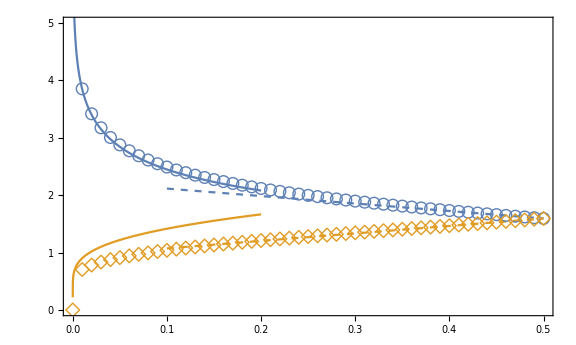

```mathematica
SizeDots=12;xm=0;xM=0.5;Δxm=0.05;ΔxM=0.1;ym=0;yM=5;Δym=0.5;ΔyM=1;
MFTPAsymptotic=Show[Plot[{2 ProductLog[3^(1/4)/(√p)],(√3)/ProductLog[3^(1/4)/(√p)]},{p,0,0.2},PlotRange->All],Plot[{(2+ProductLog[-2/ⅇ^2]-1.3017109657800467(p-1/2)),(2+ProductLog[-2/ⅇ^2]+1.3017109657800467(p-1/2))},{p,0.10,0.5},PlotRange->All,PlotStyle->{Dashed}],ListPlot[{Gp[[;;50]],Prepend[Gm[[;;50]],{0,0}]},PlotMarkers->{Style["○",Thick,SizeDots],Style["◇",Thick,SizeDots+2],PlotRange->{{0,0.5},{0,5}}},PlotLegends->Placed[{MaTeX["\\widetilde{\\alpha}_+",Magnification->SizeLegend],MaTeX["\\widetilde{\\alpha}_-",Magnification->SizeLegend]},{0.3,0.7}]],PlotRange->{{0,0.5},{0,yM}},Frame-> True,FrameLabel->{MaTeX["p",Magnification->2],MaTeX["\\widetilde{\\alpha}",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->{0.02,0.3},ImagePadding->{{70,5},{60,10}}]
```

```mathematica
Export["/Users/gregarval/Documents/Alpha_MFTP.png",MFTPAsymptotic,ImageResolution->1200]
```

/Users/gregarval/Documents/Alpha_MFTP.png

### Inset

```mathematica
<<NumericalCalculus`
```

```mathematica
<<MaTeX`
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{1,1}],{0.04,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.02,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.04,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.02,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
LTicksLog[emin_,emax_,step1_,step2_]:=Flatten[{Table[{10^i,Superscript[10,i],{0.04,0},Thickness[0.004]},{i,emin,emax,step1}],{{1,1,{0.04,0},Thickness[0.004]}},Flatten[Table[{j*10^i,"" ,{0.02,0},Thickness[0.002]},{i,emin,emax,step1},{j,step2,9,step2}],1]},1]; 

LTicksLog2[emin_,emax_,step1_,step2_]:=Flatten[{Table[{10^i,Superscript[10,i],{0.04,0},Thickness[0.004]},{i,emin,emax,step1}],Table[{10^i,"" ,{0.02,0},Thickness[0.002]},{i,emin,emax,step2}]},1];STicksLog2[emin_,emax_,step1_,step2_]:=Flatten[{Table[{10^i,,{0.04,0},Thickness[0.004]},{i,emin,emax,step1}],Table[{10^i,"" ,{0.02,0},Thickness[0.002]},{i,emin,emax,step2}]},1];
```

SetDelayed::write: Tag List in {{-Log[1000000],10,{0.02,0},Thickness[0.004]},{-Log[100000],10,{0.02,0},Thickness[0.004]},{-Log[10000],10,{0.02,0},Thickness[0.004]},{-Log[1000],10,{0.02,0},Thickness[0.004]},{-Log[100],10,{0.02,0},Thickness[0.004]},{-Log[10],10,{0.02,0},Thickness[0.004]},{0,1,{0.02,0},Thickness[0.004]},{-Log[1000000],Null,{0.01,0},Thickness[0.002]},{-Log[100000],Null,{0.01,0},Thickness[0.002]},{-Log[10000],Null,{0.01,0},Thickness[0.002]},«3»}[emin_,emax_,step1_,step2_] is Protected.

```mathematica
αmLow=Table[{N[10^i],γopt[10^i][[2]]},{i,-40,-1,1}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

```mathematica
FLow=Table[{N[10^i],Fopt[10^i]},{i,-40,-1,1}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

```mathematica
αmLow[[12]][[2]]=αmLow[[13]][[2]]/2+αmLow[[11]][[2]]/2;FLow[[12,2]]=FLow[[13,2]]/2+FLow[[11,2]]/2;
```

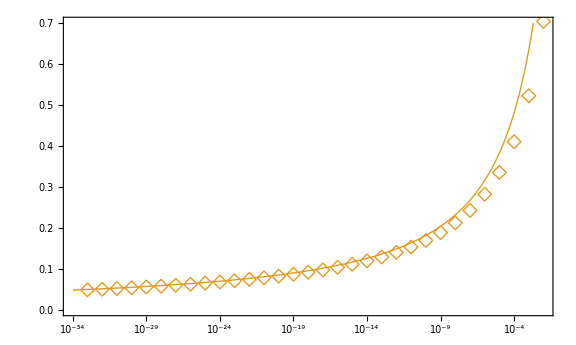

```mathematica
xm=10^-34;xM=10^-2;ym=0;yM=0.7;ΔyM=0.1;Δym=0.05;SizeDots=14;
InsetPlot=Show[LogLinearPlot[(√3)/ProductLog[3^(1/4)/(√p)],{p,xm,xM},PlotRange-> {{xm,xM},{ym,yM+0.0001}},PlotStyle->{{RGBColor[0.880722, 0.611041, 0.142051],Thick}},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],Frame->True,FrameStyle->Directive[Black,22,FontFamily->"Times New Roman",Thickness[0.004]],Exclusions-> None,FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicksLog2[-34,-2,4,1],STicksLog2[-34,-2,4,1]}}  
,FrameLabel->{MaTeX["p",Magnification->3],MaTeX["\\widetilde{\\alpha}_-",Magnification->3]} 
,ImageSize->Large,AspectRatio->0.6],ListLogLinearPlot[αmLow[[8;;]],PlotMarkers->Style["◇",RGBColor[0.880722, 0.611041, 0.142051],Thick,SizeDots]],ImageSize->Large,PlotRangePadding->None](*,Background-> RGBColor[{252,242,234,255}/255]*)
```

```mathematica
Export["/Users/gregarval/Documents/Inset_MFTP.png",InsetPlot,ImageResolution->1200]
```

/Users/gregarval/Documents/Inset_MFTP.png

## Figure 4 (MFTP Optimal)

```mathematica
<<MaTeX`
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{2,1}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

```mathematica
pPower=PowerRange[10^-70,10^-3];pVec=Range[0.00001,0.2,0.00001];
```

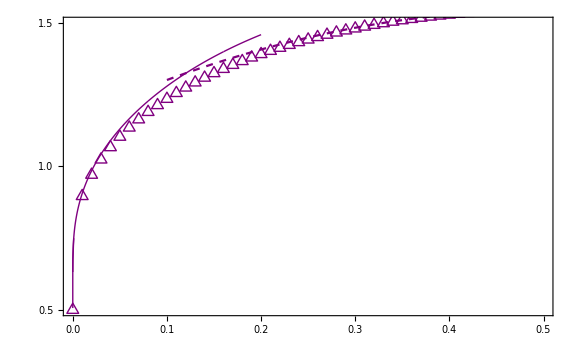

```mathematica
SizeDots=12;xm=0;xM=0.5;Δxm=0.05;ΔxM=0.1;ym=0.5;yM=1.5;Δym=0.25;ΔyM=0.5;minp=10^-40;maxp=10^-24;
MFTPOptimal=Show[ListPlot[FMatrix[[;;51]],PlotMarkers->{Style["△",Purple,Thick,SizeDots+2]}],Plot[(Cosh[1.59362]+Sinh[1.59362]-1)/(1.59362^2)-1.51757 (δp-1/2)^2,{δp,0.1,1/2},PlotStyle->{Purple,Dashed}],ListLinePlot[Transpose@{pVec,F[2 ProductLog[3^(1/4)/(√pVec)],(√3)/ProductLog[3^(1/4)/(√pVec)],pVec]},PlotStyle->{Thick,Purple},PlotRange->All],ListLinePlot[Transpose@{pPower,F[2 ProductLog[3^(1/4)/(√pPower)],(√3)/ProductLog[3^(1/4)/(√pPower)],pPower]},PlotStyle->{Thick,Purple},PlotRange->All],PlotRange->{{xm,xM},{ym,yM}},Frame-> True,FrameLabel->{MaTeX["p",Magnification->2],MaTeX["\\widetilde{\\tau}^{(1)}",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->{0.03,0.1},ImagePadding->{{70,5},{60,10}}]
```

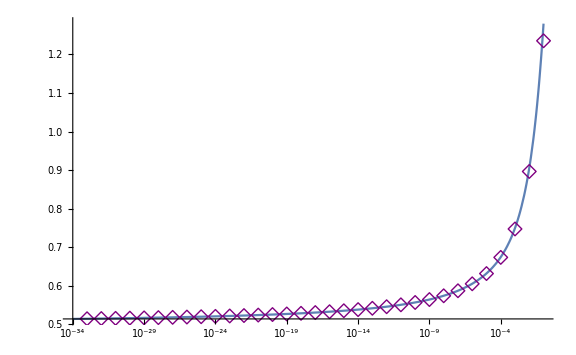

```mathematica
Show[LogLinearPlot[F[2 ProductLog[3^(1/4)/(√pzero)],(√3)/ProductLog[3^(1/4)/(√pzero)],pzero],{pzero,10^-34,0.1},PlotRange->Full],ListLogLinearPlot[FLow[[8;;]],PlotMarkers->Style["◇",Purple,Thick,SizeDots]],PlotRange->{{Log[10^-34],Log[0.1]},Automatic},ImageSize->Large,PlotRangePadding->None]
```

```mathematica
Export["/Users/gregarval/Documents/MFTP_Optimal.png",MFTPOptimal,ImageResolution->1200]
```

/Users/gregarval/Documents/MFTP_Optimal.png

## Figure 5

```mathematica
F1Plus[x_,y_]:=1/x^2(Cosh[x]+x/y Sinh[x]-1);
F1Minus[x_,y_]:=F1Plus[y,x];
F1Total[x_,y_,p_]:=p F1Plus[x,y]+(1-p)F1Minus[x,y];
F2Plus[x_,y_]:=1/(y^3 x^4)((y^2-x^2)y+(x^2-y^2(y+3))x Sinh[x]+(y^2+x^2)y Cosh[2x]-(x^2+2y-4x Sinh[x])y^2 Cosh[x]);
F2Minus[x_,y_]:=F2Plus[y,x];
F2Total[x_,y_,p_]:=p F2Plus[x,y]+(1-p)F2Minus[x,y]; 
STDTotal[x_,y_,p_]:=FullSimplify[F2Total[x,y,p]-F1Total[x,y,p]^2];
```

```mathematica
<<MaTeX`
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{2,1}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

```mathematica
Minimums=Table[{p,FindMinimum[{FullSimplify[Limit[STDTotal[γ1,γ2,pvar],{pvar->p}]],γ1>=0,γ2>=0},{{γ1,1},{γ2,1}}]},{p,0,1,0.01}];
```

```mathematica
Minimums={{0.,{-1.6709516833117366*^7,{γ1->521.7581814464655,γ2->1.081504563933127*^-6}}},{0.01,{1.0025266565694908,{γ1->2.7952856026424966,γ2->1.0430188463308414}}},{0.02,{1.1766305318945094,{γ1->2.5934631462725295,γ2->1.1318208230752238}}},{0.03,{1.2989828174827434,{γ1->2.480448797025925,γ2->1.1886824455878833}}},{0.04,{1.3958835560626157,{γ1->2.402546608233711,γ2->1.2314470634241157}}},{0.05,{1.476973971563353,{γ1->2.343411108553878,γ2->1.2661019487335154}}},{0.06,{1.5470383262187555,{γ1->2.295909566712783,γ2->1.2954375327166894}}},{0.07,{1.6088538954180274,{γ1->2.2562989187178113,γ2->1.320994777781668}}},{0.08,{1.664198977542115,{γ1->2.2223754290993623,γ2->1.3437199323027766}}},{0.09,{1.7142918238457818,{γ1->2.192734516103614,γ2->1.364238254693668}}},{0.1,{1.7600093945981066,{γ1->2.1664272237384736,γ2->1.3829857911772987}}},{0.11,{1.802007354578802,{γ1->2.142783087610843,γ2->1.4002794994115253}}},{0.12,{1.840790810814468,{γ1->2.1213112936379335,γ2->1.4163574788211986}}},{0.13,{1.876758426628373,{γ1->2.101642016490978,γ2->1.4314034481770144}}},{0.14,{1.9102312063012445,{γ1->2.083489834305235,γ2->1.445562359919803}}},{0.15,{1.9414719898990969,{γ1->2.066629961183679,γ2->1.458950756051567}}},{0.16,{1.9706990748713358,{γ1->2.050882269420547,γ2->1.4716638644051057}}},{0.17,{1.998095989741164,{γ1->2.0361002311432994,γ2->1.4837805983220949}}},{0.18,{2.023818668875838,{γ1->2.0221630703134563,γ2->1.4953671645948046}}},{0.19,{2.0480008251054023,{γ1->2.008970070039632,γ2->1.5064797220271273}}},{0.2,{2.0707580436234427,{γ1->1.9964363631758344,γ2->1.5171663767645758}}},{0.21,{2.09219094999641,{γ1->1.9844897662443255,γ2->1.5274687044726147}}},{0.22,{2.1123876955737972,{γ1->1.9730683615853553,γ2->1.5374229286210703}}},{0.23,{2.1314259314882866,{γ1->1.9621186254843554,γ2->1.5470608446263672}}},{0.24,{2.149374393902176,{γ1->1.9515939609557875,γ2->1.5564105533489279}}},{0.25,{2.1662941898285917,{γ1->1.9414535346999726,γ2->1.5654970496333769}}},{0.26,{2.182239849552195,{γ1->1.9316613456476615,γ2->1.5743426992717335}}},{0.27,{2.197260195109965,{γ1->1.9221854718996563,γ2->1.5829676291205377}}},{0.28,{2.2113990623414583,{γ1->1.9129974565634595,γ2->1.5913900489305595}}},{0.29,{2.2246959052760285,{γ1->1.9040718028007724,γ2->1.5996265189807999}}},{0.3,{2.2371863051488154,{γ1->1.8953855555234875,γ2->1.6076921743337271}}},{0.31,{2.248902401484273,{γ1->1.8869179524122623,γ2->1.6156009140997039}}},{0.32,{2.259873259009315,{γ1->1.8786501308240047,γ2->1.6233655622764755}}},{0.33,{2.2701251813446457,{γ1->1.870564880079007,γ2->1.6309980053495658}}},{0.34,{2.2796819802494155,{γ1->1.8626464308366504,γ2->1.6385093107839284}}},{0.35000000000000003,{2.2885652075004055,{γ1->1.8548802749667832,γ2->1.6459098297232402}}},{0.36,{2.2967943551557464,{γ1->1.8472530106347484,γ2->1.6532092865803185}}},{0.37,{2.304387028898543,{γ1->1.8397522083382067,γ2->1.6604168577067488}}},{0.38,{2.311359098313928,{γ1->1.8323662944332986,γ2->1.6675412409392134}}},{0.39,{2.317724827276006,{γ1->1.8250844493186382,γ2->1.6745907175104706}}},{0.4,{2.3234969870726982,{γ1->1.8178965179466369,γ2->1.6815732075664014}}},{0.41000000000000003,{2.328686954448925,{γ1->1.8107929307315755,γ2->1.6884963203333}}},{0.42,{2.33330479638062,{γ1->1.8037646332451187,γ2->1.6953673998216274}}},{0.43,{2.3373593430873174,{γ1->1.7968030233486751,γ2->1.7021935668254984}}},{0.44,{2.3408582505363644,{γ1->1.789899894621483,γ2->1.7089817578754956}}},{0.45,{2.3438080534773715,{γ1->1.7830473851133302,γ2->1.71573876172135}}},{0.46,{2.3462142098627807,{γ1->1.7762379305886487,γ2->1.7224712538565994}}},{0.47000000000000003,{2.3480811373532324,{γ1->1.7694642215411311,γ2->1.7291858295475695}}},{0.48,{2.349412242469319,{γ1->1.7627191633487207,γ2->1.7358890357909713}}},{0.49,{2.350209942829798,{γ1->1.7559958390121206,γ2->1.7425874025971773}}},{0.5,{2.3504756828070277,{γ1->1.749287473978423,γ2->1.749287473978423}}},{0.51,{2.3502099428297982,{γ1->1.7425874025971753,γ2->1.755995839012119}}},{0.52,{2.3494122424693193,{γ1->1.735889035790971,γ2->1.762719163348721}}},{0.53,{2.3480811373532324,{γ1->1.7291858295475688,γ2->1.7694642215411307}}},{0.54,{2.3462142098627807,{γ1->1.7224712538565992,γ2->1.7762379305886484}}},{0.55,{2.343808053477373,{γ1->1.7157387617213524,γ2->1.7830473851133326}}},{0.56,{2.340858250536364,{γ1->1.7089817578754987,γ2->1.7898998946214861}}},{0.5700000000000001,{2.337359343087317,{γ1->1.7021935668254948,γ2->1.796803023348672}}},{0.58,{2.33330479638062,{γ1->1.6953673998216272,γ2->1.803764633245119}}},{0.59,{2.328686954448924,{γ1->1.6884963203332997,γ2->1.8107929307315749}}},{0.6,{2.3234969870726974,{γ1->1.681573207566402,γ2->1.8178965179466373}}},{0.61,{2.3177248272760056,{γ1->1.674590717510472,γ2->1.8250844493186398}}},{0.62,{2.3113590983139276,{γ1->1.6675412409392116,γ2->1.832366294433296}}},{0.63,{2.3043870288985424,{γ1->1.66041685770675,γ2->1.839752208338208}}},{0.64,{2.2967943551557464,{γ1->1.6532092865803194,γ2->1.847253010634749}}},{0.65,{2.2885652075004037,{γ1->1.645909829723243,γ2->1.8548802749667856}}},{0.66,{2.2796819802494164,{γ1->1.6385093107839297,γ2->1.8626464308366517}}},{0.67,{2.2701251813446452,{γ1->1.6309980053495647,γ2->1.8705648800790065}}},{0.68,{2.259873259009315,{γ1->1.6233655622764767,γ2->1.8786501308240047}}},{0.6900000000000001,{2.248902401484273,{γ1->1.6156009140997047,γ2->1.886917952412263}}},{0.7000000000000001,{2.237186305148815,{γ1->1.6076921743337251,γ2->1.8953855555234855}}},{0.71,{2.2246959052760262,{γ1->1.5996265189807974,γ2->1.9040718028007704}}},{0.72,{2.2113990623414574,{γ1->1.5913900489305588,γ2->1.9129974565634595}}},{0.73,{2.197260195109965,{γ1->1.5829676291205368,γ2->1.9221854718996554}}},{0.74,{2.1822398495521957,{γ1->1.5743426992717324,γ2->1.9316613456476612}}},{0.75,{2.166294189828592,{γ1->1.5654970496333769,γ2->1.941453534699973}}},{0.76,{2.1493743939021765,{γ1->1.5564105533489274,γ2->1.9515939609557875}}},{0.77,{2.1314259314882875,{γ1->1.5470608446263678,γ2->1.9621186254843566}}},{0.78,{2.112387695573797,{γ1->1.5374229286210719,γ2->1.973068361585357}}},{0.79,{2.0921909499964095,{γ1->1.527468704472614,γ2->1.984489766244325}}},{0.8,{2.070758043623442,{γ1->1.5171663767645769,γ2->1.9964363631758364}}},{0.81,{2.0480008251054027,{γ1->1.5064797220271275,γ2->2.0089700700396325}}},{0.8200000000000001,{2.023818668875839,{γ1->1.495367164594808,γ2->2.0221630703134603}}},{0.8300000000000001,{1.9980959897411652,{γ1->1.4837805983220955,γ2->2.0361002311433007}}},{0.84,{1.9706990748713344,{γ1->1.4716638644051059,γ2->2.050882269420547}}},{0.85,{1.941471989899098,{γ1->1.4589507560515658,γ2->2.066629961183678}}},{0.86,{1.9102312063012443,{γ1->1.4455623599198044,γ2->2.083489834305236}}},{0.87,{1.8767584266283714,{γ1->1.4314034481770181,γ2->2.1016420164909815}}},{0.88,{1.8407908108144686,{γ1->1.4163574788211986,γ2->2.121311293637934}}},{0.89,{1.8020073545788007,{γ1->1.4002794994115235,γ2->2.142783087610842}}},{0.9,{1.7600093945981057,{γ1->1.3829857911773007,γ2->2.1664272237384754}}},{0.91,{1.7142918238457814,{γ1->1.3642382546936633,γ2->2.192734516103609}}},{0.92,{1.6641989775421147,{γ1->1.3437199323027775,γ2->2.222375429099363}}},{0.93,{1.6088538954180274,{γ1->1.3209947777816677,γ2->2.2562989187178117}}},{0.9400000000000001,{1.5470383262187566,{γ1->1.2954375327166887,γ2->2.295909566712782}}},{0.9500000000000001,{1.4769739715633527,{γ1->1.266101948733515,γ2->2.3434111085538767}}},{0.96,{1.3958835560626162,{γ1->1.2314470634241164,γ2->2.402546608233711}}},{0.97,{1.2989828174827447,{γ1->1.18868244558788,γ2->2.4804487970259217}}},{0.98,{1.1766305318945083,{γ1->1.1318208230752262,γ2->2.5934631462725317}}},{0.99,{1.0025266565694912,{γ1->1.0430188463308383,γ2->2.795285602642495}}},{1.,{-3.664595717979521*^7,{γ1->9.647424633294*^-7,γ2->3962.896826499163}}}};
Minimums[[1,2]]=FindMinimum[{FullSimplify[Limit[STDTotal[γ1,γ2,pvar],{pvar->0}]],γ1>=0,γ2>=0},{{γ1,1},{γ2,1}}];
Minimums[[101,2]]=FindMinimum[{FullSimplify[Limit[STDTotal[γ1,γ2,pvar],{pvar->1}]],γ1>=0,γ2>=0},{{γ1,1},{γ2,1}}];
popt=Minimums[[;;,1]];
STDOpt=Minimums[[;;,2,1]];
γ1STDOpt=Table[γ1,{p,0,1,0.01}];
γ1STDOpt=MapThread[ReplaceAll,{γ1STDOpt,Minimums[[;;,2,2,1]]}];
γ2STDOpt=Table[γ2,{p,0,1,0.01}];
γ2STDOpt=MapThread[ReplaceAll,{γ2STDOpt,Minimums[[;;,2,2,2]]}];
```

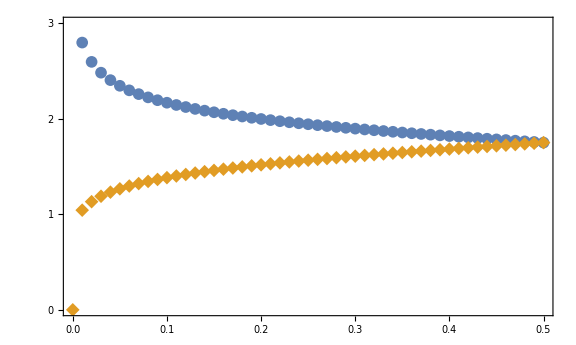

```mathematica
SizeDots=12;xm=0;xM=0.5;Δxm=0.05;ΔxM=0.1;ym=0;yM=3;Δym=0.5;ΔyM=1;SizeLegend=2;
STDAlpha=Show[ListPlot[{Transpose@{popt[[;;51]],γ1STDOpt[[;;51]]},Transpose@{popt[[;;51]],γ2STDOpt[[;;51]]}},PlotMarkers->{Style["●",Thick,SizeDots],Style["◆",Thick,SizeDots+2]},PlotLegends->Placed[{MaTeX["\\widehat{\\alpha}_+",Magnification->SizeLegend],MaTeX["\\widehat{\\alpha}_-",Magnification->SizeLegend]},{0.6,0.3}]],PlotRange->{{xm,xM},{ym,yM}},Frame-> True,FrameLabel->{MaTeX["p",Magnification->2],MaTeX["\\widehat{\\alpha}",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->{0.02,0.2},ImagePadding->{{70,5},{60,10}}]
```

```mathematica
Export["/Users/gregarval/Documents/Alpha_STD.png",STDAlpha,ImageResolution->1200]
```

/Users/gregarval/Documents/Alpha_STD.png

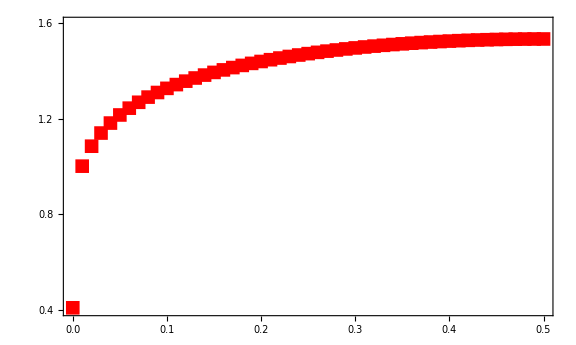

```mathematica
SizeDots=12;xm=0;xM=0.5;Δxm=0.05;ΔxM=0.1;
ym=0.4;yM=1.6;Δym=0.2;ΔyM=0.4;
STDOptimalPlot=Show[ListPlot[Transpose@{popt[[;;51]],Sqrt[STDOpt[[;;51]]]},PlotMarkers->{Style["■",Red,Thick,SizeDots+2]}],PlotRange->{{xm,xM},{ym,yM}},Frame-> True,FrameLabel->{MaTeX["p",Magnification->2],MaTeX["\\widehat{\\sigma}_{\\tau}",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->{0.02,yM/15},ImagePadding->{{70,5},{60,10}}]
```

```mathematica
Export["/Users/gregarval/Documents/STD_Optimal.png",STDOptimalPlot,ImageResolution->1200]
```

/Users/gregarval/Documents/STD_Optimal.png

### Behaviour of STD when MFTP is optimal (comparison with analytical approach)

```mathematica
<<MaTeX`

LTicksLog2[emin_,emax_,step1_,step2_]:=Flatten[{Table[{Log[10^i],Superscript[10,i],{0.02,0},Thickness[0.004]},{i,emin,emax,step1}],Table[{Log[10^i],"" ,{0.01,0},Thickness[0.002]},{i,emin,emax,step2}]},1];STicksLog2[emin_,emax_,step1_,step2_]:=Flatten[{Table[{Log[10^i],,{0.02,0},Thickness[0.004]},{i,emin,emax,step1}],Table[{Log[10^i],"" ,{0.01,0},Thickness[0.002]},{i,emin,emax,step2}]},1];
```

```mathematica
pLows=PowerRange[10^-30,0.1];alphaPLow=Table[γopt[pLows[[i]]][[1]],{i,1,Length[pLows],1}];alphaMLow=Table[γopt[pLows[[i]]][[2]],{i,1,Length[pLows],1}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

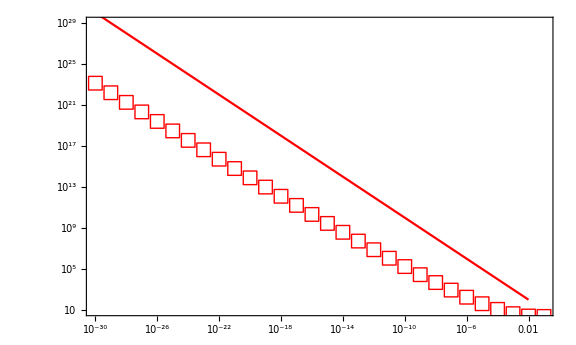

```mathematica
SizeDots=12;AppendixDPlot=Show[ListLogLogPlot[Transpose@{pLows,STDTotal[alphaPLow,alphaMLow,pLows]},PlotRange->{{10^-30,10^-1},{10,10^29}},PlotMarkers->{Style["□",Red,Thick,SizeDots+2]}],LogLogPlot[z^-1,{z,10^-30,10^-2},PlotStyle->Red],Frame->True,FrameLabel->{MaTeX["p",Magnification->2],MaTeX["\\widetilde{\\sigma}^2_{\\tau}",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicksLog2[1,29,4,1],STicksLog2[1,29,4,1]},{LTicksLog2[-30,-1,4,1],STicksLog2[-30,-1,4,1]}},ImageSize->Large,AspectRatio->0.6]
```

```mathematica
alphaPLow[[2]]=((γopt[1.1 10^-29]+γopt[0.9 10^-29])/2)[[1]];alphaMLow[[2]]=((γopt[1.1 10^-29]+γopt[0.9 10^-29])/2)[[2]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Export["/Users/gregarval/Documents/AppendixD.png",AppendixDPlot,ImageResolution->1200]
```

/Users/gregarval/Documents/AppendixD.png

## Figure 6

```mathematica
<<MaTeX`
LTicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,NumberForm[x,{2,1}],{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];

STicks[xm_,xM_,ΔxM_,Δxm_]:=Join[Table[{x,"",{0.02,0},Thickness[0.004]},{x,xm,xM,ΔxM}],Table[{x,"",{0.01,0},Thickness[0.002]},{x,xm,xM,Δxm}]];
```

Set::write: Tag Transpose in Transpose[{{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,«89»},{1.59805,1.54551,1.52915,1.52298,«3»,1.52255,1.52395,1.52545,«89»}}] is Protected.

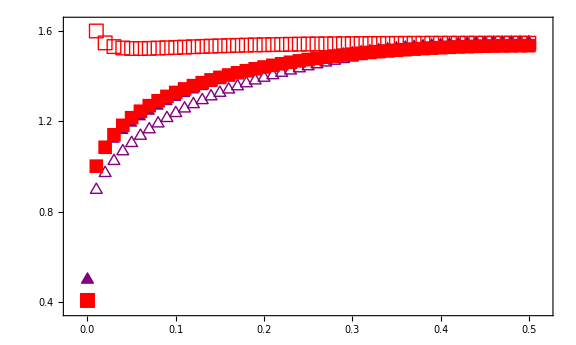

```mathematica
SizeDots=12;xm=0;xM=0.5;Δxm=0.05;ΔxM=0.1;SizeLegend=2;
ym=0.4;yM=1.6;Δym=0.1;ΔyM=0.4;List1=FMatrix[[;;51]]; List2=Transpose@{popt[[;;51]],F1Total[γ1STDOpt[[;;51]],γ2STDOpt[[;;51]],popt[[;;51]]]};
List3=PrependTo[Transpose@{Gp[[;;,1]],Sqrt[STDTotal[Gp[[;;,2]],Gm[[;;,2]],Gp[[;;,1]]]]},{0,0.408494}]; List4=Transpose@{popt,Sqrt[STDOpt]};
ComparisonMFTP=Show[ListPlot[{List1[[;;51]],List2[[;;51]],List3[[;;51]],List4[[;;51]]},PlotLegends->Placed[{MaTeX["\\widetilde{\\tau}^{(1)}",Magnification->SizeLegend],MaTeX["\\widehat{\\tau}^{(1)}",Magnification->SizeLegend],MaTeX["\\widetilde{\\sigma}_{\\tau}",Magnification->SizeLegend],MaTeX["\\widehat{\\sigma}_{\\tau}",Magnification->SizeLegend]},{0.8,0.5}]
,PlotMarkers->{Style["△",Purple,Thick,SizeDots+2],Style["▲",Purple,Thick,SizeDots+2],Style["□",Red,Thick,SizeDots+2],Style["■",Red,Thick,SizeDots+2]},PlotRange->{{-Δxm/3,xM+Δxm/3},{ym-Δym/3,yM+Δym/3}},Frame-> True,FrameLabel->{MaTeX["p",Magnification->2],MaTeX["\\tau, \\, \\sigma_{\\tau}",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->{0.01,yM/15}],ImagePadding->{{70,5},{60,10}}]
```

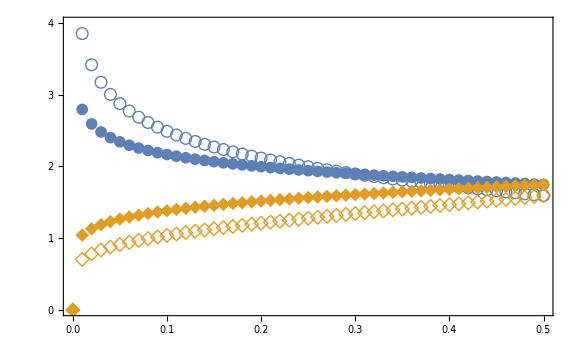

```mathematica
SizeDots=12;xm=0;xM=0.5;Δxm=0.05;ΔxM=0.1;ym=0;yM=4;Δym=0.5;ΔyM=1;SizeLegend=1.75;
ComparisonAlphas=Show[ListPlot[{Gp[[;;50]],Prepend[Gm[[;;50]],{0,0}],Transpose@{popt[[;;51]],γ1STDOpt[[;;51]]},Transpose@{popt[[;;51]],γ2STDOpt[[;;51]]}},PlotMarkers->{Style["○",RGBColor[0.368417, 0.506779, 0.709798],Thick,SizeDots],Style["◇",RGBColor[0.880722, 0.611041, 0.142051],Thick,SizeDots+2],Style["●",RGBColor[0.368417, 0.506779, 0.709798],Thick,SizeDots],Style["◆",RGBColor[0.880722, 0.611041, 0.142051],Thick,SizeDots+2]},PlotLegends->Placed[{MaTeX["\\widetilde{\\alpha}_+",Magnification->SizeLegend],MaTeX["\\widetilde{\\alpha}_-",Magnification->SizeLegend],MaTeX["\\widehat{\\alpha}_+",Magnification->SizeLegend],MaTeX["\\widehat{\\alpha}_-",Magnification->SizeLegend]},{0.7,0.75}]],PlotRange->{{xm,xM},{ym,yM}},Frame-> True,FrameLabel->{MaTeX["p",Magnification->2],MaTeX["\\alpha",Magnification->2]},Axes->None,FrameStyle->Directive[Black,20,FontFamily->"Times New Roman",Thickness[0.004]],FrameTicks->{{LTicks[ym,yM,ΔyM,Δym],STicks[ym,yM,ΔyM,Δym]},{LTicks[xm,xM,ΔxM,Δxm],STicks[xm,xM,ΔxM,Δxm]}},ImageSize->Large,AspectRatio->0.6,PlotRangePadding->{0.02,yM/15},ImagePadding->{{70,5},{60,10}}]
```

```mathematica
Export["/Users/gregarval/Documents/ComparisonOptimalAlphas.png",ComparisonAlphas,ImageResolution->1200]
```

/Users/gregarval/Documents/ComparisonOptimalAlphas.png